## CPI 200 Math Foundations of Informatics Instructor: Dianne Hansford HW 4: Visualization Due: Friday19 April by 11:58pm

## 1) Create a bivariate function called myfct[x_,y_]. Your function should be interesting: not just a plane or one of the functions we worked with already. (There will be “cool” points in the rubric!) 2) Define the domain of interest and call it xmin, xmax, ymin, ymax. Each plot below will use this domain.You must use the variables in the plot commands. 3) Complete each section in the area below the description. Leave the instructions in the nb. Guidelines: Delete all output before posting. See Cell->Delete All Output. Turn in via Canvas. Name your file lastname_HW4.nb

### PART 0 In the next cell, a test function called “testfct” is defined. This is a function with simple shape and it should be very familiar to you. A domain for this function has been defined. You must use this domain in the sections that follow. Do not change testfct or its domain. Define your own function called myfct and its domain (xmin, ymin, etc) in the cell below. For each plot in the sections below, use testfct and myfct and display together in GraphicsRow.

```mathematica
testfct[x_, y_] := x^2 + y^2;
xmint = -1; 
xmaxt = 1;
ymint = -1 ;   
ymaxt = 1;

myfct[x_, y_] := x+y^3+27;
xmin = -1;
xmax = 1;
ymin = -1;
ymax = 1;

(* Add myfct and domain definitions here *)
(*myfct[x_,y_] :=  
xmin = .... etc
*)
```

## PART 1. Plot testfct and myfct with Plot3D over D. Use the default setting for Plot3D. Put the plot for testfct in a variable called plot1a and the plot for myfct in plot1b. All cells in this HW will be done in this way. (Suppress the output of the Plot3D calls and only plot with GraphicsRow.)

```mathematica
plot1a =  Plot3D[testfct[x,y], {x, xmint, xmaxt},{y,ymint,ymaxt}];
plot1b =  Plot3D[myfct[x,y], {x, xmin, xmax},{y,ymin,ymax}];
GraphicsRow[{plot1a, plot1b}, ImageSize->Large]
```

-Graphics-

### PART 2. Plot myfct with Plot3D over D without the mesh.

```mathematica
plot2a =Plot3D[testfct[x,y], {x,xmint, xmaxt}, {y,ymint, ymaxt}, Mesh->None];
plot2b = Plot3D[myfct[x,y], {x,xmin, xmax}, {y,ymin, ymax}, Mesh->None];

GraphicsRow[{plot2a, plot2b}, ImageSize->Large]
```

-Graphics-

### PART 3. Plot the contour plot for testfct and myfct with the legend displayed

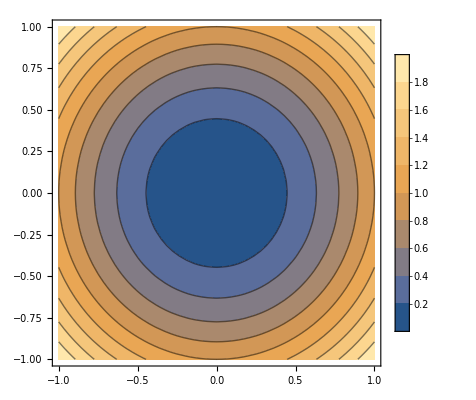

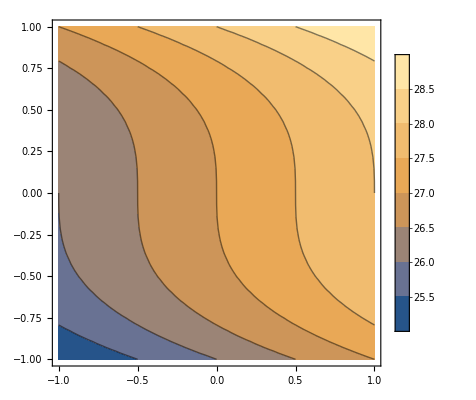

-Graphics-

```mathematica
plot3a = ContourPlot[testfct[x,y], {x, xmint, xmaxt}, {y, ymint, ymaxt}, PlotLegends->Automatic]
plot3b = ContourPlot[myfct[x,y], {x, xmin, xmax}, {y, ymin, ymax}, PlotLegends->Automatic]
GraphicsRow[{plot3a, plot3b}, ImageSize->Large]
```

### PART 4. Create contour plots of testfct = z1 and myfct = z2 for some meaningful z value that creates a curve(s) in the plot.

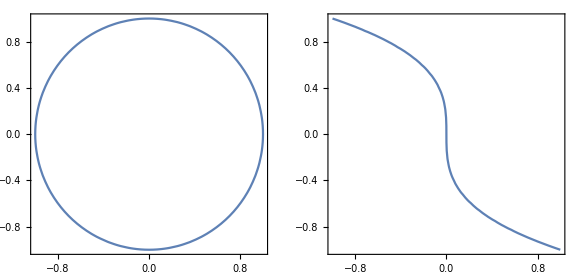

```mathematica
z1=1;
z2=27;
plot4a = ContourPlot[testfct[x,y]==z1, {x, xmint, xmaxt}, {y, ymint, ymaxt}];
plot4b = ContourPlot[myfct[x,y] == z2, {x, xmin, xmax}, {y, ymin, ymax}];
GraphicsRow[{plot4a, plot4b}, ImageSize->Large]
```

### PART 5. Create a density plot of testfct and myfct with a legend

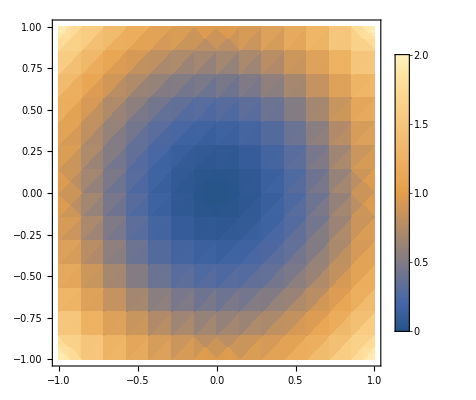

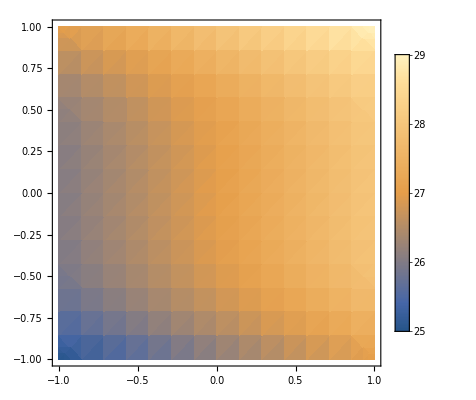

-Graphics-

```mathematica
plot5a = DensityPlot[testfct[x,y], {x,xmint, xmaxt}, {y,ymint,ymaxt}, PlotLegends->Automatic]

plot5b =DensityPlot[myfct[x,y], {x,xmin, xmax}, {y,ymin,ymax}, PlotLegends->Automatic]
GraphicsRow[{plot5a, plot5b},ImageSize->Large]
```

### PART 6. Create a scatter plot of testfct and myfct with ListPointPlot3D with 20 points in the x-direction and 20 points in the y-direction.

```mathematica
plot6a = ListPointPlot3D[Table[testfct[x,y], {x,0,20,1},{y,0,20,1}]]
plot6b = ListPointPlot3D[Table[testfct[x,y], {x,0,20,1},{y,0,20,1}]]
GraphicsRow[{plot6a, plot6b},ImageSize->Large]
```

-Graphics3D-

-Graphics3D-

-Graphics-

### PART 7. Print the gradient of testfct and myfct using MM’s Derivative function. Use the Print function and add some text to describe what is printed. Create a vector plot of testfct and myfct. Tip: See Bivariate nb

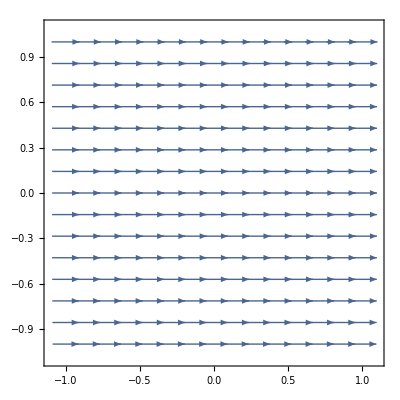

```mathematica
testfctderivative = D[testfct[x,y]];
myfctderivative= D[myfct[x,y]];
plot7a = VectorPlot[{testfctderivative,0}, {x, xmint, xmaxt}, {y,ymin, ymax}];
plot7a = VectorPlot[{myfctderivative,0}, {x, xmint, xmaxt}, {y,ymin, ymax}];
GraphicsRow[{plot7a, plot7b},ImageSize->Large]
```

### PART 8. Create a tangent plane plot on the function plot. -- See Bivariate nb for an example -- Use NMinValue and NMaxValue to find the min and max z-values. -- Add PlotRange with Full display in x and y and a z range of values that is twice the function’s range of z-values over the domain of interest. -- Add ClippingStyle->None

```mathematica
xp=0;
yp=0;
testfctdx[x_,y_]=D[testfct[x,y],x];
myfctdx[x_,y_]=D[myfct[x,y],x];
testfctdy[x_,y_]=D[testfct[x,y],y];
myfctdy[x_,y_]=D[myfct[x,y],y];
tangentplanetest[x_,y_,xp_,yp_]:=testfct[xp,yp]+testfctdx[xp,yp]*(x-xp)+testfctdy[yp,yp]*(y-yp);
tangentplane[x_,y_,xp_,yp_]:=myfct[xp,yp]+myfctdx[xp,yp]*(x-xp)+myfctdy[yp,yp]*(y-yp);
zmin=NMinValue[{testfct[x,y],x≥xmint&&x≤xmaxt&&y≥ymint&&y≤ymaxt},{x,y}];
zmax=NMaxValue[{testfct[x,y],x≥xmint&&x≤xmaxt&&y≥ymint&&y≤ymaxt},{x,y}];
Plot3D[{testfct[x,y],tangentplanetest[x,y,xp,yp]},{x,xmin,xmax},{y,ymin,ymax},PlotStyle->{Directive[Yellow,Specularity[White,200],Opacity[0.5]],Directive[Red,Specularity[White,20],Opacity[0.3]]},Mesh->None,PlotRange->Full,AxesLabel->{"x","y","f(x,y)"},ImageSize->400,PlotRange->{{xmint,xmaxt},{ymint,ymaxt},{2 (zmin),2 (zmax)}}]
```

-Graphics3D-

### Extra credit #1: Plot testfct and myfct with Plot3D and add RegionFunction to cut a circular hole in the center of the domain.

```mathematica
GraphicsRow[{plotea, ploteb},ImageSize->Large]
```

-Graphics-

### Extra credit #2: Embed the contour plot of myfct = z in Manipulate and let the z-value vary from the minimum to the maximum z-value that the function attains over the chosen domain. -- Use NMinValue and NMaxValue to find the min and max z-values. -- Print the min and max z-values for myfct along with describing text -- Initialize the plot at the mid-zvalue